# NP hard problems with Wolfram Mathematica

Author Name

Abstract

## Traveling Salesman Problem/TSP

```mathematica
europe=CountryData["Europe"];
```

```mathematica
pos=GeoPosition[CountryData[#,"CenterCoordinates"]]&/@europe;
```

```mathematica
{albania,spain}=Flatten[Position[europe,#]&/@{Entity["Country","Albania"],Entity["Country","Spain"]}];
```

```mathematica
FindShortestTour[pos,albania,spain]
```

{22149.2 km,{1,31,26,42,35,6,8,44,20,43,38,10,3,28,48,34,41,24,51,32,18,9,7,40,33,49,4,29,27,12,14,46,21,13,37,47,11,36,16,30,5,50,23,22,19,25,15,2,17,39,45}}

```mathematica
GeoGraphics[{Thick,Red,GeoPath[europe[[Last[FindShortestTour[pos,albania,spain]]]]]},GeoBackground->{"Coastlines", "VectorWeb","CountryBorders"},ImageSize->Full]
```

-Graphics-

```mathematica
GeoGraphics[{Thick,Red,GeoPath[europe⟦Last[FindShortestTour[pos,albania,spain]]⟧]},GeoScaleBar->"Metric",ImageSize->Full,GeoBackground->GeoStyling["StreetMap"]]
```

-Graphics-

```mathematica
AssociationThread[(UndirectedEdge@@@Subsequences[europe⟦Last[FindShortestTour[pos,albania,spain]]⟧,{2}])->Normal@GeoDistanceList[europe⟦Last[FindShortestTour[pos,albania,spain]]⟧]]
```

<|Albania<->North Macedonia→191.087 km,North Macedonia<->Kosovo→117.326 km,Kosovo<->Serbia→157.389 km,Serbia<->Montenegro→216.393 km,Montenegro<->Bosnia and Herzegovina→197.266 km,Bosnia and Herzegovina<->Croatia→237.104 km,Croatia<->Slovenia→118.261 km,Slovenia<->Hungary→409.324 km,Hungary<->Slovakia→189.09 km,Slovakia<->Poland→372.45 km,Poland<->Czech Republic→403.574 km,Czech Republic<->Austria→313.169 km,Austria<->Liechtenstein→287.206 km,Liechtenstein<->Switzerland→120.045 km,Switzerland<->Monaco→366.081 km,Monaco<->San Marino→407.878 km,San Marino<->Italy→126.636 km,Italy<->Vatican City→108.036 km,Vatican City<->Malta→683.299 km,Malta<->Greece→752.961 km,Greece<->Cyprus→1074.07 km,Cyprus<->Bulgaria→1125.35 km,Bulgaria<->Romania→333.366 km,Romania<->Moldova→326.506 km,Moldova<->Ukraine→315.505 km,Ukraine<->Belarus→525.988 km,Belarus<->Lithuania→422.554 km,Lithuania<->Latvia→127.243 km,Latvia<->Estonia→230.463 km,Estonia<->Finland→557.185 km,Finland<->Svalbard→1575.14 km,Svalbard<->Iceland→1909.59 km,Iceland<->Faroe Islands→640.571 km,Faroe Islands<->Norway→888.22 km,Norway<->Sweden→261.926 km,Sweden<->Denmark→727.02 km,Denmark<->Netherlands→477.841 km,Netherlands<->Germany→279.65 km,Germany<->Luxembourg→244.832 km,Luxembourg<->Belgium→195.823 km,Belgium<->United Kingdom→538.974 km,United Kingdom<->Isle of Man→165.79 km,Isle of Man<->Ireland→270.104 km,Ireland<->Guernsey→545.279 km,Guernsey<->Jersey→44.3331 km,Jersey<->France→472.125 km,France<->Andorra→390.952 km,Andorra<->Gibraltar→920.511 km,Gibraltar<->Portugal→440.49 km,Portugal<->Spain→347.252 km|>

```mathematica
GeoGraphPlot[Keys[AssociationThread[(UndirectedEdge@@@Subsequences[europe⟦Last[FindShortestTour[pos,albania,spain]]⟧,{2}])->Normal@GeoDistanceList[europe⟦Last[FindShortestTour[pos,albania,spain]]⟧]]],GraphLayout->"Driving",GeoBackground->"VectorWeb",ImageSize->Full]
```

-Graphics-

```mathematica
(UndirectedEdge@@@Subsequences[europe⟦Last[FindShortestTour[pos,albania,spain]]⟧,{2}])
```

{Albania<->North Macedonia,North Macedonia<->Kosovo,Kosovo<->Serbia,Serbia<->Montenegro,Montenegro<->Bosnia and Herzegovina,Bosnia and Herzegovina<->Croatia,Croatia<->Slovenia,Slovenia<->Hungary,Hungary<->Slovakia,Slovakia<->Poland,Poland<->Czech Republic,Czech Republic<->Austria,Austria<->Liechtenstein,Liechtenstein<->Switzerland,Switzerland<->Monaco,Monaco<->San Marino,San Marino<->Italy,Italy<->Vatican City,Vatican City<->Malta,Malta<->Greece,Greece<->Cyprus,Cyprus<->Bulgaria,Bulgaria<->Romania,Romania<->Moldova,Moldova<->Ukraine,Ukraine<->Belarus,Belarus<->Lithuania,Lithuania<->Latvia,Latvia<->Estonia,Estonia<->Finland,Finland<->Svalbard,Svalbard<->Iceland,Iceland<->Faroe Islands,Faroe Islands<->Norway,Norway<->Sweden,Sweden<->Denmark,Denmark<->Netherlands,Netherlands<->Germany,Germany<->Luxembourg,Luxembourg<->Belgium,Belgium<->United Kingdom,United Kingdom<->Isle of Man,Isle of Man<->Ireland,Ireland<->Guernsey,Guernsey<->Jersey,Jersey<->France,France<->Andorra,Andorra<->Gibraltar,Gibraltar<->Portugal,Portugal<->Spain}

```mathematica
GeoGraphPlot[,EdgeWeight->Table[TravelDistance[e[[1]],e[[2]],TravelMethod->"Driving"],{e,}],EdgeLabels->"EdgeWeight",GraphLayout->"Driving",ImageSize->Full]
```

$Aborted

```mathematica
EdgeWeight->Table[TravelDistance[e[[1]],e[[2]],TravelMethod->"Driving"],{e,}]/.{}
```

EdgeWeight→{318.937 km,173.731 km,228.767 km,360.667 km,276.059 km,323.918 km,182.436 km,537.931 km,306.965 km,505.211 km,519.132 km,444.739 km,423.54 km,179.063 km,576.521 km,587.351 km,176.175 km,147.642 km,1024.14 km,1447.91 km,2098.12 km,1761.68 km,507.302 km,471.691 km,401.924 km,753.271 km,508.99 km,172.892 km,301.512 km,682.314 km,$Failed,$Failed,$Failed,$Failed,383.713 km,1188.7 km,681.617 km,372.037 km,325.395 km,269.326 km,707.819 km,261.601 km,318.697 km,961.574 km,57.6222 km,1242.75 km,532.646 km,1187.12 km,577.877 km,415.965 km}

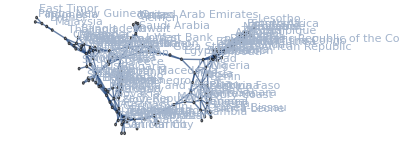

```mathematica
Eurasia=SimpleGraph@NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],13,VertexLabels->Automatic,ImageSize->Full,DirectedEdges->False]
```

```mathematica
EulerianGraphQ[Eurasia]
```

False

```mathematica
FindHamiltonianCycle[Eurasia]
```

{}

```mathematica
FindHamiltonianPath[Eurasia]
```

{}

```mathematica
FindIndependentEdgeSet[Eurasia]
```

{Switzerland<->Liechtenstein,Austria<->Hungary,France<->Andorra,Germany<->Denmark,Italy<->Vatican City,Czech Republic<->Poland,Slovakia<->Ukraine,Slovenia<->Croatia,Belgium<->Netherlands,Spain<->Gibraltar,Romania<->Moldova,Serbia<->Kosovo,Belarus<->Lithuania,Russia<->Mongolia,Morocco<->Algeria,Latvia<->Estonia,Bosnia and Herzegovina<->Montenegro,Western Sahara<->Mauritania,Bulgaria<->Greece,Azerbaijan<->Georgia,China<->Nepal,Kazakhstan<->Turkmenistan,North Korea<->South Korea,Norway<->Sweden,North Macedonia<->Albania,Libya<->Tunisia,Mali<->Burkina Faso,Niger<->Chad,Armenia<->Turkey,Iran<->Pakistan,Afghanistan<->Uzbekistan,Bhutan<->India,Kyrgyzstan<->Tajikistan,Laos<->Thailand,Myanmar<->Bangladesh,Vietnam<->Cambodia,Iraq<->Kuwait,Egypt<->Gaza Strip,Sudan<->Eritrea,Guinea<->Guinea-Bissau,Ivory Coast<->Ghana,Senegal<->Gambia,Benin<->Togo,Nigeria<->Cameroon,Syria<->Lebanon,Central African Republic<->South Sudan,Israel<->Jordan,Liberia<->Sierra Leone,Saudi Arabia<->Qatar,Ethiopia<->Djibouti,Malaysia<->Brunei,Equatorial Guinea<->Gabon,Republic of the Congo<->Angola,Democratic Republic of the Congo<->Uganda,Kenya<->Somalia,Indonesia<->East Timor,Oman<->United Arab Emirates,Burundi<->Rwanda,Tanzania<->Malawi,Zambia<->Zimbabwe,Namibia<->Botswana,Mozambique<->Eswatini,South Africa<->Lesotho}

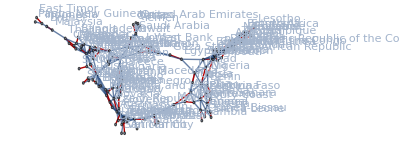

```mathematica
HighlightGraph[Graph[{Entity["Country", "Switzerland"], Entity["Country", "Austria"], Entity["Country", "France"], Entity["Country", "Germany"], Entity["Country", "Italy"], Entity["Country", "Liechtenstein"], Entity["Country", "CzechRepublic"], Entity["Country", "Hungary"], Entity["Country", "Slovakia"], Entity["Country", "Slovenia"], Entity["Country", "Andorra"], Entity["Country", "Belgium"], Entity["Country", "Luxembourg"], Entity["Country", "Monaco"], Entity["Country", "Spain"], Entity["Country", "Denmark"], Entity["Country", "Netherlands"], Entity["Country", "Poland"], Entity["Country", "SanMarino"], Entity["Country", "VaticanCity"], Entity["Country", "Croatia"], Entity["Country", "Romania"], Entity["Country", "Serbia"], Entity["Country", "Ukraine"], Entity["Country", "Belarus"], Entity["Country", "Lithuania"], Entity["Country", "Russia"], Entity["Country", "Gibraltar"], Entity["Country", "Morocco"], Entity["Country", "Portugal"], Entity["Country", "Latvia"], Entity["Country", "BosniaHerzegovina"], Entity["Country", "Montenegro"], Entity["Country", "Algeria"], Entity["Country", "WesternSahara"], Entity["Country", "Bulgaria"], Entity["Country", "Moldova"], Entity["Country", "Azerbaijan"], Entity["Country", "China"], Entity["Country", "Estonia"], Entity["Country", "Finland"], Entity["Country", "Georgia"], Entity["Country", "Kazakhstan"], Entity["Country", "Mongolia"], Entity["Country", "NorthKorea"], Entity["Country", "Norway"], Entity["Country", "Kosovo"], Entity["Country", "Macedonia"], Entity["Country", "Libya"], Entity["Country", "Mali"], Entity["Country", "Mauritania"], Entity["Country", "Niger"], Entity["Country", "Tunisia"], Entity["Country", "Armenia"], Entity["Country", "Iran"], Entity["Country", "Turkey"], Entity["Country", "Greece"], Entity["Country", "Afghanistan"], Entity["Country", "Bhutan"], Entity["Country", "India"], Entity["Country", "Kyrgyzstan"], Entity["Country", "Laos"], Entity["Country", "Myanmar"], Entity["Country", "Nepal"], Entity["Country", "Pakistan"], Entity["Country", "Tajikistan"], Entity["Country", "Vietnam"], Entity["Country", "Sweden"], Entity["Country", "Turkmenistan"], Entity["Country", "Uzbekistan"], Entity["Country", "Albania"], Entity["Country", "SouthKorea"], Entity["Country", "Bangladesh"], Entity["Country", "Iraq"], Entity["Country", "Cambodia"], Entity["Country", "Thailand"], Entity["Country", "Chad"], Entity["Country", "Egypt"], Entity["Country", "Sudan"], Entity["Country", "BurkinaFaso"], Entity["Country", "Guinea"], Entity["Country", "IvoryCoast"], Entity["Country", "Senegal"], Entity["Country", "Benin"], Entity["Country", "Nigeria"], Entity["Country", "Syria"], Entity["Country", "Togo"], Entity["Country", "Ghana"], Entity["Country", "Cameroon"], Entity["Country", "CentralAfricanRepublic"], Entity["Country", "GazaStrip"], Entity["Country", "Israel"], Entity["Country", "GuineaBissau"], Entity["Country", "Liberia"], Entity["Country", "SierraLeone"], Entity["Country", "Jordan"], Entity["Country", "Kuwait"], Entity["Country", "SaudiArabia"], Entity["Country", "Gambia"], Entity["Country", "Eritrea"], Entity["Country", "Ethiopia"], Entity["Country", "SouthSudan"], Entity["Country", "Lebanon"], Entity["Country", "Malaysia"], Entity["Country", "EquatorialGuinea"], Entity["Country", "Gabon"], Entity["Country", "RepublicCongo"], Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "Djibouti"], Entity["Country", "Kenya"], Entity["Country", "Somalia"], Entity["Country", "WestBank"], Entity["Country", "Brunei"], Entity["Country", "Indonesia"], Entity["Country", "Oman"], Entity["Country", "Qatar"], Entity["Country", "UnitedArabEmirates"], Entity["Country", "Yemen"], Entity["Country", "Uganda"], Entity["Country", "Angola"], Entity["Country", "Burundi"], Entity["Country", "Rwanda"], Entity["Country", "Tanzania"], Entity["Country", "Zambia"], Entity["Country", "EastTimor"], Entity["Country", "PapuaNewGuinea"], Entity["Country", "Namibia"], Entity["Country", "Malawi"], Entity["Country", "Mozambique"], Entity["Country", "Botswana"], Entity["Country", "Zimbabwe"], Entity["Country", "SouthAfrica"], Entity["Country", "Swaziland"], Entity["Country", "Lesotho"]}, {UndirectedEdge[Entity["Country", "Hungary"], Entity["Country", "Croatia"]], UndirectedEdge[Entity["Country", "Austria"], Entity["Country", "Hungary"]], UndirectedEdge[Entity["Country", "Guinea"], Entity["Country", "IvoryCoast"]], UndirectedEdge[Entity["Country", "Syria"], Entity["Country", "Jordan"]], UndirectedEdge[Entity["Country", "Vietnam"], Entity["Country", "Cambodia"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Kazakhstan"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Vietnam"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Mongolia"]], UndirectedEdge[Entity["Country", "Iraq"], Entity["Country", "Jordan"]], UndirectedEdge[Entity["Country", "Iraq"], Entity["Country", "Syria"]], UndirectedEdge[Entity["Country", "Poland"], Entity["Country", "Belarus"]], UndirectedEdge[Entity["Country", "Austria"], Entity["Country", "CzechRepublic"]], UndirectedEdge[Entity["Country", "CzechRepublic"], Entity["Country", "Poland"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Bhutan"]], UndirectedEdge[Entity["Country", "Poland"], Entity["Country", "Lithuania"]], UndirectedEdge[Entity["Country", "Belarus"], Entity["Country", "Lithuania"]], UndirectedEdge[Entity["Country", "Guinea"], Entity["Country", "Liberia"]], UndirectedEdge[Entity["Country", "IvoryCoast"], Entity["Country", "Liberia"]], UndirectedEdge[Entity["Country", "IvoryCoast"], Entity["Country", "Ghana"]], UndirectedEdge[Entity["Country", "Belgium"], Entity["Country", "Netherlands"]], UndirectedEdge[Entity["Country", "Kazakhstan"], Entity["Country", "Turkmenistan"]], UndirectedEdge[Entity["Country", "Kosovo"], Entity["Country", "Macedonia"]], UndirectedEdge[Entity["Country", "Macedonia"], Entity["Country", "Greece"]], UndirectedEdge[Entity["Country", "Malawi"], Entity["Country", "Mozambique"]], UndirectedEdge[Entity["Country", "Mozambique"], Entity["Country", "Swaziland"]], UndirectedEdge[Entity["Country", "Mozambique"], Entity["Country", "Zimbabwe"]], UndirectedEdge[Entity["Country", "Andorra"], Entity["Country", "Spain"]], UndirectedEdge[Entity["Country", "Spain"], Entity["Country", "Gibraltar"]], UndirectedEdge[Entity["Country", "Spain"], Entity["Country", "Morocco"]], UndirectedEdge[Entity["Country", "Morocco"], Entity["Country", "WesternSahara"]], UndirectedEdge[Entity["Country", "WesternSahara"], Entity["Country", "Mauritania"]], UndirectedEdge[Entity["Country", "Croatia"], Entity["Country", "BosniaHerzegovina"]], UndirectedEdge[Entity["Country", "Poland"], Entity["Country", "Russia"]], UndirectedEdge[Entity["Country", "Belarus"], Entity["Country", "Russia"]], UndirectedEdge[Entity["Country", "Lithuania"], Entity["Country", "Russia"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "China"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Estonia"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Kazakhstan"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Mongolia"]], UndirectedEdge[Entity["Country", "Gabon"], Entity["Country", "RepublicCongo"]], UndirectedEdge[Entity["Country", "Armenia"], Entity["Country", "Iran"]], UndirectedEdge[Entity["Country", "Iran"], Entity["Country", "Iraq"]], UndirectedEdge[Entity["Country", "Iran"], Entity["Country", "Turkmenistan"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "NorthKorea"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "NorthKorea"]], UndirectedEdge[Entity["Country", "NorthKorea"], Entity["Country", "SouthKorea"]], UndirectedEdge[Entity["Country", "Djibouti"], Entity["Country", "Somalia"]], UndirectedEdge[Entity["Country", "Zambia"], Entity["Country", "Malawi"]], UndirectedEdge[Entity["Country", "Zambia"], Entity["Country", "Mozambique"]], UndirectedEdge[Entity["Country", "Zambia"], Entity["Country", "Namibia"]], UndirectedEdge[Entity["Country", "Zambia"], Entity["Country", "Zimbabwe"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Norway"]], UndirectedEdge[Entity["Country", "Norway"], Entity["Country", "Sweden"]], UndirectedEdge[Entity["Country", "Malaysia"], Entity["Country", "Brunei"]], UndirectedEdge[Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "RepublicCongo"]], UndirectedEdge[Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "Rwanda"]], UndirectedEdge[Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "Zambia"]], UndirectedEdge[Entity["Country", "Mauritania"], Entity["Country", "Senegal"]], UndirectedEdge[Entity["Country", "Guinea"], Entity["Country", "Senegal"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Georgia"]], UndirectedEdge[Entity["Country", "Georgia"], Entity["Country", "Armenia"]], UndirectedEdge[Entity["Country", "Libya"], Entity["Country", "Niger"]], UndirectedEdge[Entity["Country", "Libya"], Entity["Country", "Tunisia"]], UndirectedEdge[Entity["Country", "Georgia"], Entity["Country", "Turkey"]], UndirectedEdge[Entity["Country", "Armenia"], Entity["Country", "Turkey"]], UndirectedEdge[Entity["Country", "Greece"], Entity["Country", "Turkey"]], UndirectedEdge[Entity["Country", "Iran"], Entity["Country", "Turkey"]], UndirectedEdge[Entity["Country", "Turkey"], Entity["Country", "Iraq"]], UndirectedEdge[Entity["Country", "Turkey"], Entity["Country", "Syria"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Afghanistan"]], UndirectedEdge[Entity["Country", "Afghanistan"], Entity["Country", "Iran"]], UndirectedEdge[Entity["Country", "Afghanistan"], Entity["Country", "Turkmenistan"]], UndirectedEdge[Entity["Country", "Austria"], Entity["Country", "Liechtenstein"]], UndirectedEdge[Entity["Country", "Belarus"], Entity["Country", "Latvia"]], UndirectedEdge[Entity["Country", "Lithuania"], Entity["Country", "Latvia"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Latvia"]], UndirectedEdge[Entity["Country", "Estonia"], Entity["Country", "Latvia"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Azerbaijan"]], UndirectedEdge[Entity["Country", "Azerbaijan"], Entity["Country", "Armenia"]], UndirectedEdge[Entity["Country", "Azerbaijan"], Entity["Country", "Georgia"]], UndirectedEdge[Entity["Country", "Azerbaijan"], Entity["Country", "Iran"]], UndirectedEdge[Entity["Country", "Azerbaijan"], Entity["Country", "Turkey"]], UndirectedEdge[Entity["Country", "Cambodia"], Entity["Country", "Thailand"]], UndirectedEdge[Entity["Country", "Thailand"], Entity["Country", "Malaysia"]], UndirectedEdge[Entity["Country", "Libya"], Entity["Country", "Egypt"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Nepal"]], UndirectedEdge[Entity["Country", "Croatia"], Entity["Country", "Montenegro"]], UndirectedEdge[Entity["Country", "BosniaHerzegovina"], Entity["Country", "Montenegro"]], UndirectedEdge[Entity["Country", "Kosovo"], Entity["Country", "Montenegro"]], UndirectedEdge[Entity["Country", "Ethiopia"], Entity["Country", "Djibouti"]], UndirectedEdge[Entity["Country", "Ethiopia"], Entity["Country", "Somalia"]], UndirectedEdge[Entity["Country", "Ethiopia"], Entity["Country", "Kenya"]], UndirectedEdge[Entity["Country", "Kenya"], Entity["Country", "Somalia"]], UndirectedEdge[Entity["Country", "EquatorialGuinea"], Entity["Country", "Gabon"]], UndirectedEdge[Entity["Country", "Iraq"], Entity["Country", "Kuwait"]], UndirectedEdge[Entity["Country", "Cameroon"], Entity["Country", "EquatorialGuinea"]], UndirectedEdge[Entity["Country", "Cameroon"], Entity["Country", "Gabon"]], UndirectedEdge[Entity["Country", "Cameroon"], Entity["Country", "RepublicCongo"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Myanmar"]], UndirectedEdge[Entity["Country", "Myanmar"], Entity["Country", "Bangladesh"]], UndirectedEdge[Entity["Country", "Myanmar"], Entity["Country", "Thailand"]], UndirectedEdge[Entity["Country", "Ghana"], Entity["Country", "Togo"]], UndirectedEdge[Entity["Country", "Spain"], Entity["Country", "Portugal"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Kyrgyzstan"]], UndirectedEdge[Entity["Country", "Kazakhstan"], Entity["Country", "Kyrgyzstan"]], UndirectedEdge[Entity["Country", "Hungary"], Entity["Country", "Romania"]], UndirectedEdge[Entity["Country", "Romania"], Entity["Country", "Moldova"]], UndirectedEdge[Entity["Country", "Egypt"], Entity["Country", "Israel"]], UndirectedEdge[Entity["Country", "Syria"], Entity["Country", "Israel"]], UndirectedEdge[Entity["Country", "Israel"], Entity["Country", "Jordan"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "India"]], UndirectedEdge[Entity["Country", "Bhutan"], Entity["Country", "India"]], UndirectedEdge[Entity["Country", "India"], Entity["Country", "Bangladesh"]], UndirectedEdge[Entity["Country", "India"], Entity["Country", "Myanmar"]], UndirectedEdge[Entity["Country", "India"], Entity["Country", "Nepal"]], UndirectedEdge[Entity["Country", "Romania"], Entity["Country", "Bulgaria"]], UndirectedEdge[Entity["Country", "Bulgaria"], Entity["Country", "Greece"]], UndirectedEdge[Entity["Country", "Bulgaria"], Entity["Country", "Macedonia"]], UndirectedEdge[Entity["Country", "Bulgaria"], Entity["Country", "Turkey"]], UndirectedEdge[Entity["Country", "Syria"], Entity["Country", "Lebanon"]], UndirectedEdge[Entity["Country", "Israel"], Entity["Country", "Lebanon"]], UndirectedEdge[Entity["Country", "Kosovo"], Entity["Country", "Albania"]], UndirectedEdge[Entity["Country", "Macedonia"], Entity["Country", "Albania"]], UndirectedEdge[Entity["Country", "Montenegro"], Entity["Country", "Albania"]], UndirectedEdge[Entity["Country", "Albania"], Entity["Country", "Greece"]], UndirectedEdge[Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "Burundi"]], UndirectedEdge[Entity["Country", "Burundi"], Entity["Country", "Rwanda"]], UndirectedEdge[Entity["Country", "Oman"], Entity["Country", "UnitedArabEmirates"]], UndirectedEdge[Entity["Country", "Oman"], Entity["Country", "Yemen"]], UndirectedEdge[Entity["Country", "Belgium"], Entity["Country", "Luxembourg"]], UndirectedEdge[Entity["Country", "Mali"], Entity["Country", "Guinea"]], UndirectedEdge[Entity["Country", "Mali"], Entity["Country", "IvoryCoast"]], UndirectedEdge[Entity["Country", "Mali"], Entity["Country", "Mauritania"]], UndirectedEdge[Entity["Country", "Mali"], Entity["Country", "Niger"]], UndirectedEdge[Entity["Country", "Mali"], Entity["Country", "Senegal"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Pakistan"]], UndirectedEdge[Entity["Country", "Afghanistan"], Entity["Country", "Pakistan"]], UndirectedEdge[Entity["Country", "India"], Entity["Country", "Pakistan"]], UndirectedEdge[Entity["Country", "Iran"], Entity["Country", "Pakistan"]], UndirectedEdge[Entity["Country", "Hungary"], Entity["Country", "Serbia"]], UndirectedEdge[Entity["Country", "Croatia"], Entity["Country", "Serbia"]], UndirectedEdge[Entity["Country", "Romania"], Entity["Country", "Serbia"]], UndirectedEdge[Entity["Country", "Serbia"], Entity["Country", "BosniaHerzegovina"]], UndirectedEdge[Entity["Country", "Serbia"], Entity["Country", "Bulgaria"]], UndirectedEdge[Entity["Country", "Serbia"], Entity["Country", "Kosovo"]], UndirectedEdge[Entity["Country", "Serbia"], Entity["Country", "Macedonia"]], UndirectedEdge[Entity["Country", "Serbia"], Entity["Country", "Montenegro"]], UndirectedEdge[Entity["Country", "Malaysia"], Entity["Country", "Indonesia"]], UndirectedEdge[Entity["Country", "Indonesia"], Entity["Country", "PapuaNewGuinea"]], UndirectedEdge[Entity["Country", "Kazakhstan"], Entity["Country", "Uzbekistan"]], UndirectedEdge[Entity["Country", "Afghanistan"], Entity["Country", "Uzbekistan"]], UndirectedEdge[Entity["Country", "Kyrgyzstan"], Entity["Country", "Uzbekistan"]], UndirectedEdge[Entity["Country", "Turkmenistan"], Entity["Country", "Uzbekistan"]], UndirectedEdge[Entity["Country", "Senegal"], Entity["Country", "Gambia"]], UndirectedEdge[Entity["Country", "Libya"], Entity["Country", "Sudan"]], UndirectedEdge[Entity["Country", "Egypt"], Entity["Country", "Sudan"]], UndirectedEdge[Entity["Country", "Sudan"], Entity["Country", "Ethiopia"]], UndirectedEdge[Entity["Country", "Austria"], Entity["Country", "Italy"]], UndirectedEdge[Entity["Country", "Italy"], Entity["Country", "SanMarino"]], UndirectedEdge[Entity["Country", "Switzerland"], Entity["Country", "Austria"]], UndirectedEdge[Entity["Country", "Switzerland"], Entity["Country", "Italy"]], UndirectedEdge[Entity["Country", "Switzerland"], Entity["Country", "Liechtenstein"]], UndirectedEdge[Entity["Country", "Sudan"], Entity["Country", "Eritrea"]], UndirectedEdge[Entity["Country", "Eritrea"], Entity["Country", "Djibouti"]], UndirectedEdge[Entity["Country", "Eritrea"], Entity["Country", "Ethiopia"]], UndirectedEdge[Entity["Country", "Israel"], Entity["Country", "WestBank"]], UndirectedEdge[Entity["Country", "Jordan"], Entity["Country", "WestBank"]], UndirectedEdge[Entity["Country", "Iraq"], Entity["Country", "SaudiArabia"]], UndirectedEdge[Entity["Country", "Jordan"], Entity["Country", "SaudiArabia"]], UndirectedEdge[Entity["Country", "Kuwait"], Entity["Country", "SaudiArabia"]], UndirectedEdge[Entity["Country", "SaudiArabia"], Entity["Country", "Oman"]], UndirectedEdge[Entity["Country", "SaudiArabia"], Entity["Country", "Qatar"]], UndirectedEdge[Entity["Country", "SaudiArabia"], Entity["Country", "UnitedArabEmirates"]], UndirectedEdge[Entity["Country", "SaudiArabia"], Entity["Country", "Yemen"]], UndirectedEdge[Entity["Country", "Switzerland"], Entity["Country", "France"]], UndirectedEdge[Entity["Country", "France"], Entity["Country", "Andorra"]], UndirectedEdge[Entity["Country", "France"], Entity["Country", "Belgium"]], UndirectedEdge[Entity["Country", "France"], Entity["Country", "Italy"]], UndirectedEdge[Entity["Country", "France"], Entity["Country", "Luxembourg"]], UndirectedEdge[Entity["Country", "France"], Entity["Country", "Monaco"]], UndirectedEdge[Entity["Country", "France"], Entity["Country", "Spain"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Finland"]], UndirectedEdge[Entity["Country", "Finland"], Entity["Country", "Norway"]], UndirectedEdge[Entity["Country", "Finland"], Entity["Country", "Sweden"]], UndirectedEdge[Entity["Country", "Niger"], Entity["Country", "Nigeria"]], UndirectedEdge[Entity["Country", "Nigeria"], Entity["Country", "Cameroon"]], UndirectedEdge[Entity["Country", "Austria"], Entity["Country", "Slovakia"]], UndirectedEdge[Entity["Country", "CzechRepublic"], Entity["Country", "Slovakia"]], UndirectedEdge[Entity["Country", "Hungary"], Entity["Country", "Slovakia"]], UndirectedEdge[Entity["Country", "Poland"], Entity["Country", "Slovakia"]], UndirectedEdge[Entity["Country", "Austria"], Entity["Country", "Slovenia"]], UndirectedEdge[Entity["Country", "Italy"], Entity["Country", "Slovenia"]], UndirectedEdge[Entity["Country", "Hungary"], Entity["Country", "Slovenia"]], UndirectedEdge[Entity["Country", "Slovenia"], Entity["Country", "Croatia"]], UndirectedEdge[Entity["Country", "Indonesia"], Entity["Country", "EastTimor"]], UndirectedEdge[Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "Uganda"]], UndirectedEdge[Entity["Country", "Kenya"], Entity["Country", "Uganda"]], UndirectedEdge[Entity["Country", "Uganda"], Entity["Country", "Rwanda"]], UndirectedEdge[Entity["Country", "Sudan"], Entity["Country", "SouthSudan"]], UndirectedEdge[Entity["Country", "Ethiopia"], Entity["Country", "SouthSudan"]], UndirectedEdge[Entity["Country", "SouthSudan"], Entity["Country", "DemocraticRepublicCongo"]], UndirectedEdge[Entity["Country", "SouthSudan"], Entity["Country", "Kenya"]], UndirectedEdge[Entity["Country", "SouthSudan"], Entity["Country", "Uganda"]], UndirectedEdge[Entity["Country", "Niger"], Entity["Country", "Benin"]], UndirectedEdge[Entity["Country", "Benin"], Entity["Country", "Nigeria"]], UndirectedEdge[Entity["Country", "Benin"], Entity["Country", "Togo"]], UndirectedEdge[Entity["Country", "Mali"], Entity["Country", "BurkinaFaso"]], UndirectedEdge[Entity["Country", "Niger"], Entity["Country", "BurkinaFaso"]], UndirectedEdge[Entity["Country", "Benin"], Entity["Country", "BurkinaFaso"]], UndirectedEdge[Entity["Country", "BurkinaFaso"], Entity["Country", "Ghana"]], UndirectedEdge[Entity["Country", "BurkinaFaso"], Entity["Country", "IvoryCoast"]], UndirectedEdge[Entity["Country", "BurkinaFaso"], Entity["Country", "Togo"]], UndirectedEdge[Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "Tanzania"]], UndirectedEdge[Entity["Country", "Kenya"], Entity["Country", "Tanzania"]], UndirectedEdge[Entity["Country", "Uganda"], Entity["Country", "Tanzania"]], UndirectedEdge[Entity["Country", "Burundi"], Entity["Country", "Tanzania"]], UndirectedEdge[Entity["Country", "Rwanda"], Entity["Country", "Tanzania"]], UndirectedEdge[Entity["Country", "Tanzania"], Entity["Country", "Malawi"]], UndirectedEdge[Entity["Country", "Tanzania"], Entity["Country", "Mozambique"]], UndirectedEdge[Entity["Country", "Tanzania"], Entity["Country", "Zambia"]], UndirectedEdge[Entity["Country", "Egypt"], Entity["Country", "GazaStrip"]], UndirectedEdge[Entity["Country", "GazaStrip"], Entity["Country", "Israel"]], UndirectedEdge[Entity["Country", "Switzerland"], Entity["Country", "Germany"]], UndirectedEdge[Entity["Country", "Austria"], Entity["Country", "Germany"]], UndirectedEdge[Entity["Country", "France"], Entity["Country", "Germany"]], UndirectedEdge[Entity["Country", "Germany"], Entity["Country", "Belgium"]], UndirectedEdge[Entity["Country", "Germany"], Entity["Country", "CzechRepublic"]], UndirectedEdge[Entity["Country", "Germany"], Entity["Country", "Denmark"]], UndirectedEdge[Entity["Country", "Germany"], Entity["Country", "Luxembourg"]], UndirectedEdge[Entity["Country", "Germany"], Entity["Country", "Netherlands"]], UndirectedEdge[Entity["Country", "Germany"], Entity["Country", "Poland"]], UndirectedEdge[Entity["Country", "Zambia"], Entity["Country", "Botswana"]], UndirectedEdge[Entity["Country", "Botswana"], Entity["Country", "Namibia"]], UndirectedEdge[Entity["Country", "Botswana"], Entity["Country", "Zimbabwe"]], UndirectedEdge[Entity["Country", "Libya"], Entity["Country", "Chad"]], UndirectedEdge[Entity["Country", "Niger"], Entity["Country", "Chad"]], UndirectedEdge[Entity["Country", "Chad"], Entity["Country", "Cameroon"]], UndirectedEdge[Entity["Country", "Chad"], Entity["Country", "Nigeria"]], UndirectedEdge[Entity["Country", "Chad"], Entity["Country", "Sudan"]], UndirectedEdge[Entity["Country", "Morocco"], Entity["Country", "Algeria"]], UndirectedEdge[Entity["Country", "Algeria"], Entity["Country", "Libya"]], UndirectedEdge[Entity["Country", "Algeria"], Entity["Country", "Mali"]], UndirectedEdge[Entity["Country", "Algeria"], Entity["Country", "Mauritania"]], UndirectedEdge[Entity["Country", "Algeria"], Entity["Country", "Niger"]], UndirectedEdge[Entity["Country", "Algeria"], Entity["Country", "Tunisia"]], UndirectedEdge[Entity["Country", "Algeria"], Entity["Country", "WesternSahara"]], UndirectedEdge[Entity["Country", "Hungary"], Entity["Country", "Ukraine"]], UndirectedEdge[Entity["Country", "Poland"], Entity["Country", "Ukraine"]], UndirectedEdge[Entity["Country", "Slovakia"], Entity["Country", "Ukraine"]], UndirectedEdge[Entity["Country", "Belarus"], Entity["Country", "Ukraine"]], UndirectedEdge[Entity["Country", "Romania"], Entity["Country", "Ukraine"]], UndirectedEdge[Entity["Country", "Russia"], Entity["Country", "Ukraine"]], UndirectedEdge[Entity["Country", "Ukraine"], Entity["Country", "Moldova"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Laos"]], UndirectedEdge[Entity["Country", "Laos"], Entity["Country", "Cambodia"]], UndirectedEdge[Entity["Country", "Laos"], Entity["Country", "Myanmar"]], UndirectedEdge[Entity["Country", "Laos"], Entity["Country", "Thailand"]], UndirectedEdge[Entity["Country", "Laos"], Entity["Country", "Vietnam"]], UndirectedEdge[Entity["Country", "Botswana"], Entity["Country", "SouthAfrica"]], UndirectedEdge[Entity["Country", "Mozambique"], Entity["Country", "SouthAfrica"]], UndirectedEdge[Entity["Country", "Namibia"], Entity["Country", "SouthAfrica"]], UndirectedEdge[Entity["Country", "Zimbabwe"], Entity["Country", "SouthAfrica"]], UndirectedEdge[Entity["Country", "SouthAfrica"], Entity["Country", "Lesotho"]], UndirectedEdge[Entity["Country", "SouthAfrica"], Entity["Country", "Swaziland"]], UndirectedEdge[Entity["Country", "Guinea"], Entity["Country", "GuineaBissau"]], UndirectedEdge[Entity["Country", "Senegal"], Entity["Country", "GuineaBissau"]], UndirectedEdge[Entity["Country", "China"], Entity["Country", "Tajikistan"]], UndirectedEdge[Entity["Country", "Afghanistan"], Entity["Country", "Tajikistan"]], UndirectedEdge[Entity["Country", "Kyrgyzstan"], Entity["Country", "Tajikistan"]], UndirectedEdge[Entity["Country", "Tajikistan"], Entity["Country", "Uzbekistan"]], UndirectedEdge[Entity["Country", "DemocraticRepublicCongo"], Entity["Country", "Angola"]], UndirectedEdge[Entity["Country", "RepublicCongo"], Entity["Country", "Angola"]], UndirectedEdge[Entity["Country", "Angola"], Entity["Country", "Namibia"]], UndirectedEdge[Entity["Country", "Angola"], Entity["Country", "Zambia"]], UndirectedEdge[Entity["Country", "Guinea"], Entity["Country", "SierraLeone"]], UndirectedEdge[Entity["Country", "Liberia"], Entity["Country", "SierraLeone"]], UndirectedEdge[Entity["Country", "Chad"], Entity["Country", "CentralAfricanRepublic"]], UndirectedEdge[Entity["Country", "Sudan"], Entity["Country", "CentralAfricanRepublic"]], UndirectedEdge[Entity["Country", "Cameroon"], Entity["Country", "CentralAfricanRepublic"]], UndirectedEdge[Entity["Country", "CentralAfricanRepublic"], Entity["Country", "DemocraticRepublicCongo"]], UndirectedEdge[Entity["Country", "CentralAfricanRepublic"], Entity["Country", "RepublicCongo"]], UndirectedEdge[Entity["Country", "CentralAfricanRepublic"], Entity["Country", "SouthSudan"]], UndirectedEdge[Entity["Country", "Italy"], Entity["Country", "VaticanCity"]]}, {ImageSize -> Full, VertexLabels -> {Automatic}}],%427]
```